```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
Rawdata = Import["E:\\DropBox\\Overig\\Wikipedia//Opwarming van de Aarde//labrijn_ea.dat", "Table"][[23;;-3]];
```

```mathematica
Yearlydata=Rawdata[[All,{1,14}]];
Yearlydata=Table[{Yearlydata[[i,1]], Yearlydata[[i,2]]/10}, {i, 1, Length[Yearlydata]}];
Lopendgemiddelde = Table[{Yearlydata[[i,1]],Mean[Yearlydata[[i-5;;i+5,2]]]}, {i, 6,Length[Yearlydata]-6}];
Plottrend = ListPlot[Lopendgemiddelde, Joined -> True, PlotStyle -> {Thick, Red}];
```

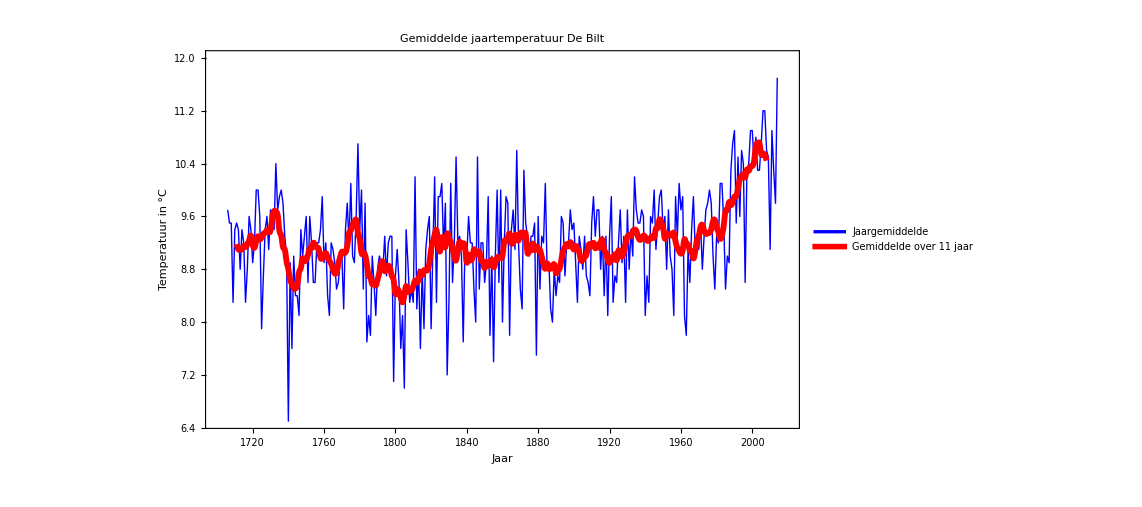

```mathematica
Plotdata = ListLinePlot[{Yearlydata, Lopendgemiddelde}, PlotStyle -> {{Blue}, {Red, Thickness[0.005]}}, InterpolationOrder->{1,2},PlotLegends -> {Placed[LineLegend[{Directive[Blue, Thickness[0.12]]},{Style["Jaargemiddelde", FontSize ->40]}],{0.59,0.15}],
 Placed[LineLegend[{Directive[Large,Red, Thickness[0.20]]},{Style["Gemiddelde over 11 jaar", FontSize -> 40]}], {0.69, 0.06}]},Frame -> True, FrameLabel -> {"Jaar", "Temperatuur in °C"}, FrameStyle ->Directive[40, Thick],  AspectRatio -> 0.60, PlotRange -> {{1700, 2020}, {6.5, 12.0}}, PlotLabel -> Text[Style["Gemiddelde jaartemperatuur De Bilt", FontSize ->40]]]
```

```mathematica
Export["E:\\DropBox\\Overig\\Wikipedia\\Opwarming van de Aarde\\DeBilt3.png",Plotdata,"png"]
```

E:\DropBox\Overig\Wikipedia\Opwarming van de Aarde\DeBilt3.png

```mathematica
Plotopmaak= Plot[9,{x,1700,2080}, PlotStyle -> {{White}, {Red, Thick}},Frame -> True, FrameLabel -> {"Jaar", "Temperatuur in °C"}, FrameStyle ->Directive[40, Thick],  AspectRatio -> 0.60, PlotRange -> {{1700, 2020}, {6.5, 11.5}}, PlotLabel -> Text[Style["Gemiddelde jaartemperatuur De Bilt", FontSize ->40]]];
```

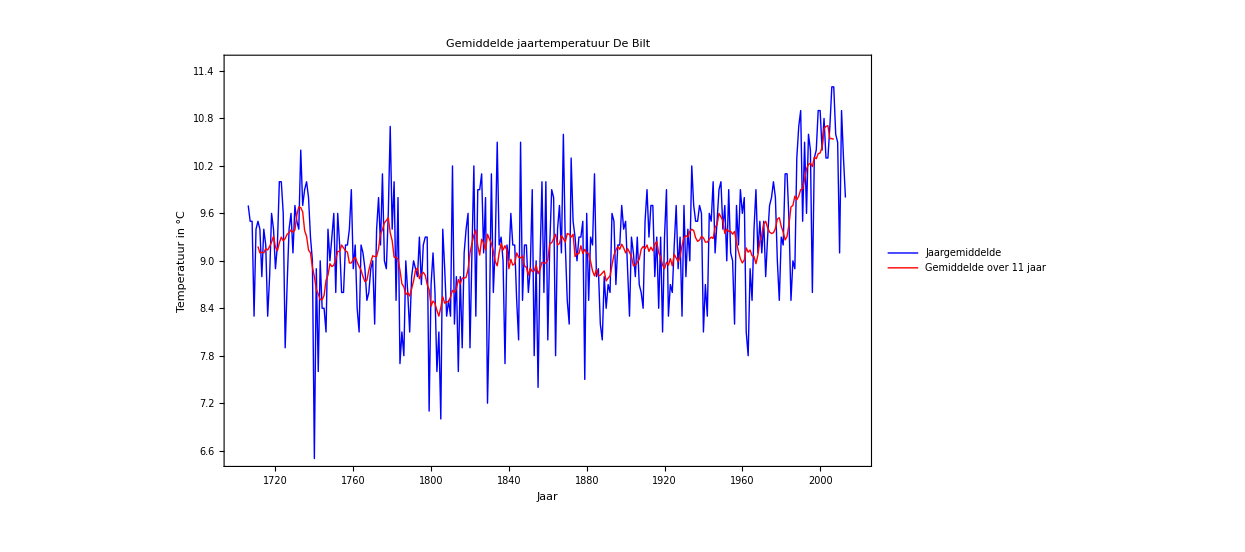

```mathematica
Show[Plotopmaak,Plotdata]
```

```mathematica
Export["E://Dropbox//Wikipedia//Opwarming van de Aarde//Temperaturewithouttitle.pdf",%77,"PDF"]
```

E://Dropbox//Wikipedia//Opwarming van de Aarde//Temperaturewithouttitle.pdf